```mathematica
numberOfAgents = 100;
donationCost = -10;
buyCost = -40;
donationHealthChange=7;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.3,
RandomReal[0.05], (* Prob to buy tool *)
RandomReal[0.2], (* Prob to donate *)
0, (* Has tool (tool health) *)
0 (* payoff *)
}],numberOfAgents];
```

Calculate payoff now has a max number of tools so that a player that donates doesn’t have to if the pool is full.

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_,maxPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd &&maxPTools<=nPTools,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3]
```

CalculatePayoff[{0,0,1,5,0},3]

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(*distance/4)+*)0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.1]
MutateAgent[agent_]:=Module[
{p=agent[[1]],pb=agent[[2]],pd=agent[[3]]},
{p,MutateValue[pb],MutateValue[pd],0,0}
];
```

0.172563

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {},
maxPoolTools=Length[agentList]*1.2},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
(*agents=RandomSample[agents];*)
agents=Sort[agents,#1[[3]]>#2[[3]]&];
For[j=1,j≤Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools,maxPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=If[healthChange==-1,healthChange,nPoolTools]; (* this is completely bonkers *)
];

PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];
```

Simulation clears pool health after each round. This means that mutated agents start with a new pool.

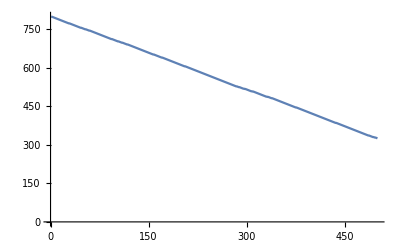

{{0.3,0.198887,1,3,240},{0.3,0.18954,1,0,238},{0.3,0.0495224,1,6,234},{0.3,1,0.0157576,0,225},{0.3,1,0.0969871,0,225},{0.3,1,0.153558,0,225},{0.3,0.0495224,1,0,222},{0.3,0.18954,1,4,221},{0.3,1,0.0157576,1,220},{0.3,0.90025,0.183228,1,219},{0.3,0.325065,1,3,219},{0.3,0.0495224,1,0,219},{0.3,0.18954,1,1,219},{0.3,0.88727,0.267126,2,214},{0.3,1,0.070379,3,210},{0.3,1,0.0969871,0,210},{0.3,1,0.124237,0,210},{0.3,1,0,1,205},{0.3,1,0.124237,1,205},{0.3,1,0.124237,1,205},{0.3,1,0.124237,4,205},{0.3,0.899668,0.120133,1,204},{0.3,0.899668,0.120133,2,204},{0.3,1,0.070379,5,200},{0.3,1,0.070379,5,200},{0.3,1,0.124237,2,200},{0.3,1,0.124237,5,200},{0.3,0.92686,0.14042,8,200},{0.3,1,0.309029,8,200},{0.3,0.90025,0.183228,8,199},{0.3,0.884961,0.302328,2,199},{0.3,0.198887,1,1,198},{0.3,0.18954,1,7,198},{0.3,1,0.070379,6,195},{0.3,1,0.070379,6,195},{0.3,1,0.070379,0,195},{0.3,1,0.070379,6,195},{0.3,1,0.183554,9,195},{0.3,0.721029,0.260084,2,195},{0.3,0.90025,0.183228,6,194},{0.3,0.88727,0.267126,0,194},{0.3,0.213089,1,0,194},{0.3,0.0495224,1,7,193},{0.3,0.90025,0.183228,1,189},{0.3,0.213089,1,2,187},{0.3,0.198887,1,8,186},{0.3,1,0.0157576,2,185},{0.3,1,0.0561948,5,185},{0.3,1,0.070379,2,185},{0.3,1,0.070379,2,185},{0.3,1,0.124237,8,185},{0.3,1,0.153558,2,185},{0.3,1,0.309029,5,185},{0.3,1,0.309029,2,185},{0.3,0.198887,1,0,185},{0.3,0.90025,0.183228,8,183},{0.3,0.0495224,1,4,182},{0.3,1,0.0157576,9,180},{0.3,1,0.070379,6,180},{0.3,1,0.0969871,9,180},{0.3,1,0.124237,9,180},{0.3,0.90025,0.183228,3,179},{0.3,0.18954,1,0,179},{0.3,0.90025,0.183228,9,178},{0.3,0.721029,0.260084,9,178},{0.3,0.901822,0.267107,9,176},{0.3,1,0,10,175},{0.3,1,0.0157576,4,175},{0.3,1,0.0561948,7,175},{0.3,1,0.070379,10,175},{0.3,1,0.070379,1,175},{0.3,1,0.0969871,4,175},{0.3,1,0.124237,7,175},{0.3,1,0.124237,7,175},{0.3,1,0.124237,4,175},{0.3,1,0.124237,10,175},{0.3,1,0.309029,7,175},{0.3,0.952371,0.0550083,10,174},{0.3,1,0.0157576,8,170},{0.3,0.89679,0.0838248,5,170},{0.3,1,0.0969871,8,170},{0.3,1,0.0969871,8,170},{0.3,1,0.124237,8,170},{0.3,1,0.309029,5,170},{0.3,0.213089,1,8,169},{0.3,0.89679,0.0838248,5,168},{0.3,0.18954,1,2,168},{0.3,0.213089,1,1,167},{0.3,1,0.0157576,9,165},{0.3,1,0.070379,9,165},{0.3,1,0.0969871,6,165},{0.3,1,0.124237,6,165},{0.3,0.90025,0.183228,3,163},{0.3,1,0.309029,4,160},{0.3,1,0.070379,8,155},{0.3,1,0.124237,8,155},{0.3,0.325065,1,7,138},{0.3,0.198887,1,10,136},{0.3,0.0495224,1,1,131},{0.3,0.198887,1,0,127}}

```mathematica
RunSim[agentList_]:=Module[{agents=agentList,history={}},
For[k=1,k<100,k++,
{ag, ph} =DoRound[agents,800,500];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Append[history, ph];
];
{ag, ph} =DoRound[agents,800,500];
history=Append[history, ph];
{ag, history}
];

{a,h}=RunSim[agentParams];
ListLinePlot[h[[-1]]]
Sort[a,Last[#1]>Last[#2]&]
```

Simulation runs with agents mutating while pool is still functioning. Now if a lot of people donated in the past a new mutation can take advantage of this and vice versa.

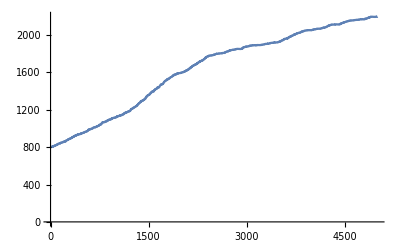

{{0.3,0.0266406,0.0751156,0,85},{0.3,0.0266406,0.0751156,0,57},{0.3,0.604085,0,1,54},{0.3,0.540523,0,1,45},{0.3,0.334409,0,0,44},{0.3,0.592792,0,1,44},{0.3,0.604085,0,0,43},{0.3,0.473379,0,0,43},{0.3,0.578028,0,0,43},{0.3,0.604085,0,0,43},{0.3,0.0266406,0.0751156,0,43},{0.3,0.537926,0,0,42},{0.3,0.527376,0,1,40},{0.3,0.592792,0,1,38},{0.3,0.592792,0,1,35},{0.3,0.592792,0,2,35},{0.3,0.592792,0,2,34},{0.3,0.0266406,0.0751156,0,34},{0.3,0.371302,0,3,33},{0.3,0.592792,0,2,33},{0.3,0.473379,0,2,33},{0.3,0.0266406,0.0751156,0,32},{0.3,0.592792,0,3,30},{0.3,0.540523,0,3,30},{0.3,0.527376,0,0,30},{0.3,0.380151,0,0,30},{0.3,0.578028,0,3,29},{0.3,0.334409,0,6,29},{0.3,0.527376,0,3,29},{0.3,0.592792,0,3,27},{0.3,0.578028,0,0,27},{0.3,0.334409,0,5,26},{0.3,0.592792,0,0,26},{0.3,0.578028,0,4,25},{0.3,0.473379,0,0,25},{0.3,0.578028,0,4,24},{0.3,0.371302,0,0,24},{0.3,0.592792,0,4,24},{0.3,0.592792,0,1,24},{0.3,0.592792,0,4,23},{0.3,0.540523,0,4,22},{0.3,0.380151,0,4,22},{0.3,0.592792,0,4,22},{0.3,0.334409,0,4,22},{0.3,0.334409,0,1,22},{0.3,0.538347,0,7,22},{0.3,0.540523,0,4,22},{0.3,0.592792,0,2,21},{0.3,0.473379,0,5,20},{0.3,0.604085,0,2,20},{0.3,0.592792,0,5,20},{0.3,0.592792,0,5,19},{0.3,0.592792,0,5,19},{0.3,0.592792,0,5,19},{0.3,0.527376,0,5,19},{0.3,0.592792,0,5,19},{0.3,0.578028,0,5,19},{0.3,0.578028,0,5,19},{0.3,0.592792,0,5,19},{0.3,0.604085,0,6,19},{0.3,0.369277,0.0414434,4,19},{0.3,0.592792,0,5,18},{0.3,0.334409,0,1,15},{0.3,0.578028,0,6,15},{0.3,0.578028,0,6,15},{0.3,0.527376,0,9,14},{0.3,0.527376,0,6,14},{0.3,0.371302,0,6,13},{0.3,0.380151,0,6,13},{0.3,0.342928,0.0228169,2,12},{0.3,0.334409,0,6,11},{0.3,0.592792,0,7,9},{0.3,0.538347,0,3,9},{0.3,0.334409,0,7,8},{0.3,0.380151,0,7,7},{0.3,0.540523,0,7,7},{0.3,0.530961,0.051168,8,7},{0.3,0.592792,0,8,3},{0.3,0,0.0556244,0,3},{0.3,0.578028,0,8,2},{0.3,0.527376,0,8,2},{0.3,0.371302,0,8,2},{0.3,0.540523,0,8,2},{0.3,0.538347,0,8,1},{0.3,0.592792,0,9,-2},{0.3,0.592792,0,9,-2},{0.3,0.578028,0,9,-3},{0.3,0.455711,0,10,-4},{0.3,0.540523,0,9,-5},{0.3,0.380151,0,8,-5},{0.3,0.380151,0,9,-5},{0.3,0.592792,0,10,-7},{0.3,0.527376,0,9,-8},{0.3,0.592792,0,10,-9},{0.3,0.604085,0,10,-9},{0.3,0.592792,0,10,-10},{0.3,0.538347,0,10,-11},{0.3,0.540523,0,10,-13},{0.3,0.578028,0,10,-15},{0.3,0.623321,0.208822,6,-60}}

```mathematica
RunSimContinuous[agentList_,initHealth_]:=Module[{agents=agentList,history={},poolHealth=initHealth},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,poolHealth,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Join[history, ph];
poolHealth=ph[[-1]];
];
{ag, ph} =DoRound[agents,poolHealth,100];
history=Join[history, ph];
{ag, history}
];

{a,h}=RunSimContinuous[agentParams,8000];
ListLinePlot[Map[Function[x, x/fullToolHealth],h]](* plot the number of tools in the pool at any given time *)
Sort[a,Last[#1]>Last[#2]&]
```

In the above example we see a working pool where agents buy tools seldom and borrow more often. We also see that the pool is kept running by a few volunteers, everyone is not donating to the pool.